{(-1+x) x,(-1+x) x^2,(-1+x) x^3,(-1+x) x^4,(-1+x) x^5,(-1+x) x^6}

{{0.39328,0.19664,0.135712,0.105248,0.0901972,0.0828531},{0.19664,0.168992,0.138528,0.118613,0.106405,0.0990774},{0.135712,0.138528,0.128085,0.118181,0.110757,0.1056},{0.105248,0.118613,0.118181,0.11465,0.110986,0.107953},{0.0901972,0.106405,0.110757,0.110986,0.10988,0.108471},{0.0828531,0.0990774,0.1056,0.107953,0.108471,0.10819}}

{-0.08,-0.04672,-0.03008,-0.020608,-0.01472,-0.0108268}

{-0.0937095,-0.496347,0.40126}

Dot::dotsh: Tensors {-0.0937095,-0.496347,0.40126} and {-0.0000204282,-4.17318×10^-10,-8.52521×10^-15,-1.74158×10^-19,-3.5578×10^-24,-7.26807×10^-29} have incompatible shapes.

Dot::dotsh: Tensors {-0.0937095,-0.496347,0.40126} and {-0.0200113,-0.000408802,-8.35125×10^-6,-1.70604×10^-7,-3.4852×10^-9,-7.11978×10^-11} have incompatible shapes.

Dot::dotsh: Tensors {-0.0937095,-0.496347,0.40126} and {-0.0391691,-0.00159954,-0.00006532,-2.66746×10^-6,-1.0893×10^-7,-4.44836×10^-9} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

-Graphics-

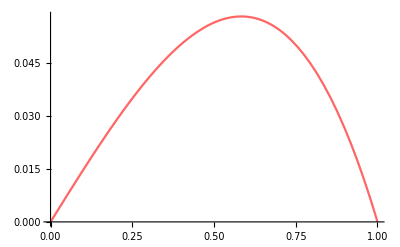

-Graphics-

```mathematica
Tn[f_,{a_,b_,m_}]:=0.5*((b-a)/m)*(f[a]+f[b]+Sum[2*f[a+(i*(b-a))/m],{i,1,m-1}])
ϕ=Table[x^i*(x-1),{i,1,6}]
K=Table[Tn[D[ϕ[[j]],x]*D[ϕ[[n]],x]+ϕ[[j]]*ϕ[[n]]/.x->#&,0,1,5],{j,6},{n,6}]
F=Table[Tn[x*ϕ[[j]]/.x->#&,0,1,5],{j,1,6}]
W=LinearSolve[K1,F1]
Uh[x_]:=W.ϕ
G1=Plot[Uh1[x],{x,0,1},ImageSize->400,AxesStyle->Black]
G2=Plot[x-Sinh[x]/Sinh[1],{x,0,1},PlotStyle->{Red,Opacity[0.6]}]
G3=Show[G2,G1,PlotRange->All,ImageSize->400,AxesStyle->Black]
```

1a)

```mathematica
A=Table[i*j/(i+j-1)-((1+i)j+(1+j)*i)/(i+j)+(1+(1+i)(1+j))/(i+j+1)-2/(i+j+2)+1/(i+j+3),{i,3},{j,3}]
```

```mathematica
{{11/30,11/60,23/210},{11/60,1/7,89/840},{23/210,89/840,113/1260}}//MatrixForm
```

(11/30 | 11/60 | 23/210
11/60 | 1/7 | 89/840
23/210 | 89/840 | 113/1260)

```mathematica
K//MatrixForm
```

(0.39328 | 0.19664 | 0.135712
0.19664 | 0.168992 | 0.138528
0.135712 | 0.138528 | 0.128085)

```mathematica
Diagonal[K]-Diagonal[A]
```

{0.0266133,0.0261349,0.0384027}